```mathematica
(* Clear["Global`*"]*)
```

```mathematica
(* Basic test for functions defined in Program.nb *)
(* Run Program.nb first before running this notebook *)
(* Tests may take substantial time to complete. For efficiency, run specific sections of this notebook instead of running the entire notebook *)
```

```mathematica
(*****************************************)
(* The metric and change of variables *)
(*****************************************)
```

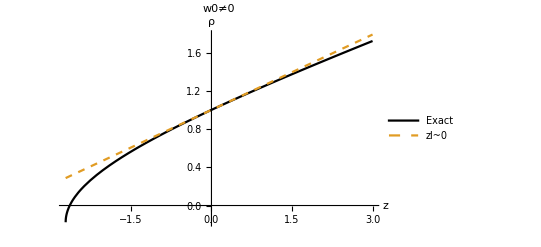

```mathematica
(* plot rho as a function of zl *)
(* Mark characteristic points and plot asymptotics, with ϵ=a*z*)
w00=1; (* case w0≠0, ρ≃w0+ϵ/t0 *)
a00=0.2;
Plot[{z2Rho[zl,w00,a00],w00+a00*zl/Tanh[w00]},{zl,zlT[w00,a00],3},GridLines->{{zlC[w00,a00]}, {w00,RhoT[w00]}},AxesLabel->{"z","ρ"},PlotStyle->{Black,Dashed},PlotLabel->"w0≠0",PlotLegends->{"Exact","zl~0"}]
```

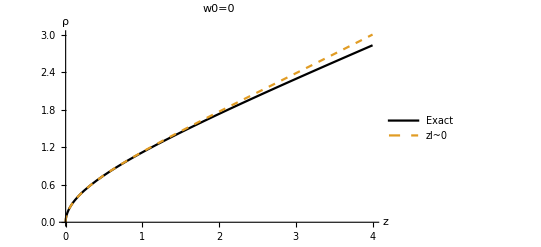

```mathematica
(* case w0=0, ρ≃√2ϵ(1+ϵ/4) *)
a00=0.5;
Plot[{z2Rho[zl,0,a00],Sqrt[2a00*zl](1+a00*zl/4)},{zl,zlT[0,a00],4},GridLines->{{zlC[0,a00]}, None},AxesLabel->{"z","ρ"},PlotStyle->{Black,Dashed},PlotLabel->"w0=0",PlotLegends->{"Exact","zl~0"}]
```

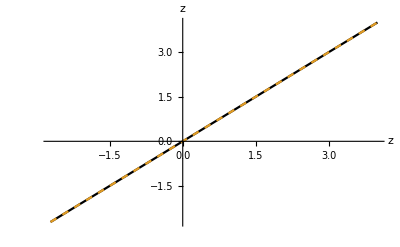

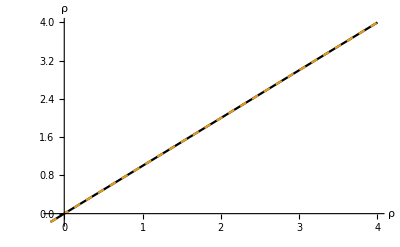

```mathematica
(* Check coordinate inversion between z and ρ *)
w00=1; 
a00=0.2;
Plot[{r2Z[z2Rho[zl,w00,a00],w00,a00],zl},{zl,zlT[w00,a00],4},AxesLabel->{"z","z"},PlotStyle->{Black,Dashed}]
Plot[{z2Rho[r2Z[r,w00,a00],w00,a00],r},{r,RhoT[w00],4},AxesLabel->{"ρ","ρ"},PlotStyle->{Black,Dashed}]
```

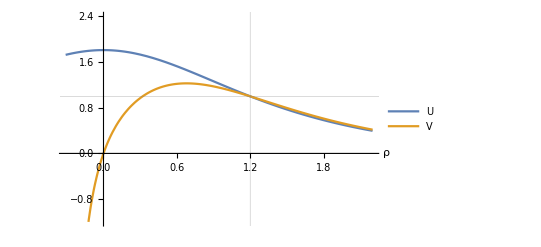

```mathematica
(* Plot U,V as function of ρ *)
w00=1.2;
Plot[{U[r,w00],V[r,w00]},{r,RhoT[w00],1+w00},GridLines->{{w00},{1}},PlotRange->{-w00,2w00},AxesLabel->{"ρ"},PlotLegends->{"U","V"}]
```

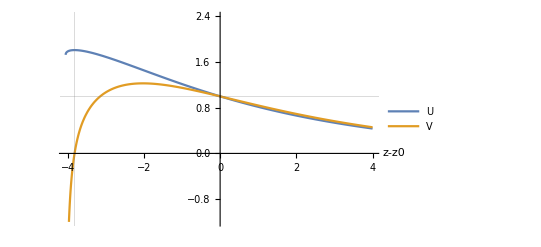

```mathematica
(* Plot U,V as function of z *)
w00=1.2;
a00=0.2;
Plot[{Uz[zl,w00,a00],Vz[zl,w00,a00]},{zl,zlT[w00,a00],4},GridLines->{{zlC[w00,a00]},{1}},PlotRange->{-w00,2w00},AxesLabel->{"z-z0"},PlotLegends->{"U","V"}]
```

```mathematica
(* asymptotics of U/V *)
UVasympt[ah_,w0_]:=Piecewise[{{1-ah/Cosh[w0]/(1+Cosh[w0]),w0≠0},{1-ah/3,w0==0}}]
UVasympt[ah,w0]
```

Piecewise[{{1-(ah Sech[w0])/(1+Cosh[w0]), w0≠0}, {1-ah/3, w0==0}, {0, True}}]

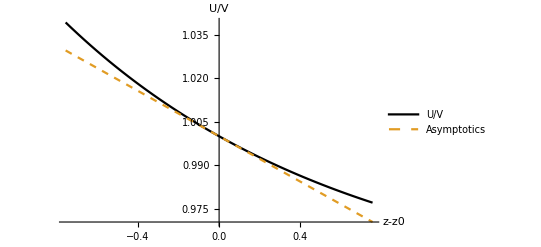

```mathematica
(* Plot U/V and asymptotics as functions of z *)
w00=1.2;
a00=0.2;
zmax=Sinh[w00]/a00/10;
Plot[{Uz[zl,w00,a00]/Vz[zl,w00,a00],UVasympt[a00*zl,w00]},{zl,-zmax,zmax},AxesLabel->{"z-z0","U/V"},PlotLegends->{"U/V","Asymptotics"},PlotStyle->{Black,Dashed}]
```

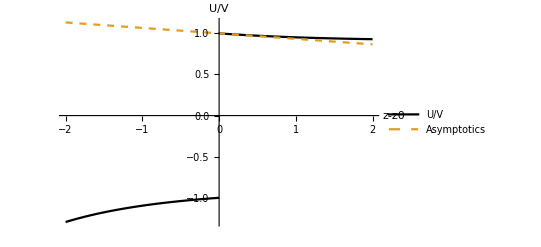

```mathematica
(* w0=0 *)
a00=0.2;
zmax=2;
Plot[{Uz[zl,0,a00]/Vz[zl,0,a00],UVasympt[a00*zl,0]},{zl,-zmax,zmax},AxesLabel->{"z-z0","U/V"},PlotLegends->{"U/V","Asymptotics"},PlotStyle->{Black,Dashed}]
```

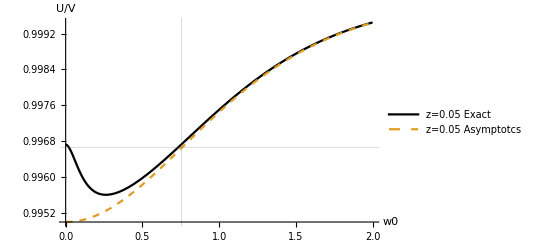

```mathematica
zl0=0.05;
Plot[{Uz[zl0,w0,a00]/Vz[zl0,w0,a00],UVasympt[a00*zl0,w0]},{w0,0,2},AxesLabel->{"w0","U/V"},PlotStyle->{Black,Dashed},PlotLegends->{Row[{"z=",zl0," Exact"}],Row[{"z=",zl0," Asymptotcs"}]},GridLines->{{Sinh[w00]/a00/10}, {UVasympt[a00*zl0,0]}}]
```

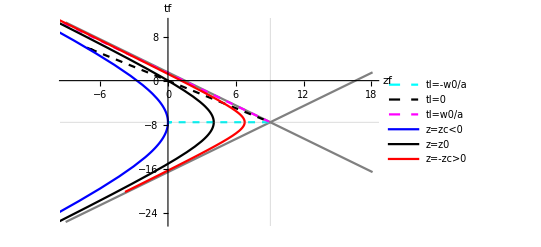

```mathematica
(* Change of coordinates *)
(* plot characteristic lines in (tf,zf) frame *)
w00=1.2;
a0=0.2; (* a0 cannot be zero *)
(* Derived parameters *)
c0=Cosh[w00];
s0=Sinh[w00];
(* Bounds of axis *)
z0=c0/a0;
zc0=zlC[w00,a0];
(* Rindler horizons *)
pl=Plot[{zf-(c0+s0)/a0,-zf+(c0-s0)/a0},{zf,-z0,2z0},GridLines->{{z0}, {-s0/a0}},PlotStyle->Gray,AxesLabel->{"zf","tf"}];
(* Lines for tl= -w0/a0, 0, and +w0/a0 *)
pt=ParametricPlot[{{ZF[-w00/a0,zl,w00,a0],TF[-w00/a0,zl,w00,a0]},{ZF[0,zl,w00,a0],TF[0,zl,w00,a0]},{ZF[w00/a0,zl,w00,a0],TF[w00/a0,zl,w00,a0]}},{zl,-z0,3z0},PlotStyle->{Directive[Dashed,Cyan],Directive[Dashed,Black],Directive[Dashed,Magenta]},PlotLegends->{"tl=-w0/a","tl=0","tl=w0/a"}];
(* Lines for z= zc<0, z0, and -zc>0 *)
pz=ParametricPlot[{{ZF[tl,zc0,w00,a0],TF[tl,zc0,w00,a0]},{ZF[tl,0,w00,a0],TF[tl,0,w00,a0]},{ZF[tl,-zc0,w00,a0],TF[tl,-zc0,w00,a0]}},{tl,-2z0,2z0},PlotStyle->{Blue,Black,Red},PlotLegends->{"z=zc<0","z=z0","z=-zc>0"}];
Show[pl,pt,pz]
```

```mathematica
(* Change of coordinates *)
(* plot characteristic lines in (tl,zl) frame *)
```

```mathematica
(* Plot lines where tf is constant *)
PlotTF[tf_,w0_,a_,style_,legend_]:=Module[
{zfmax,zfmin,p},
(* upper bound of zf limited by Rindler horizon *)
zfmax=zfRindler[tf,w0,a];
(* lower bound taken to be characteristic scale *)
zfmin=Cosh[w0]/a;
p=ParametricPlot[{ZL[tf,zf,w00,a0],TL[tf,zf,w00,a0]},{zf,zfmin,zfmax(1-10^(-3))},PlotStyle->style,PlotLegends->{legend}];
Return[p]
]
```

```mathematica
(* Plot lines where zf is constant *)
PlotZF[zf_,w0_,a_,style_,legend_]:=Module[
{tfmax,tfmin,p},
(* upper bound of zf limited by Rindler horizon *)
tfmax=tfRindler[zf,w0,a];
(* lower bound taken to be characteristic scale *)
tfmin=-Sinh[w0]/a;
p=ParametricPlot[{ZL[tf,zf,w00,a0],TL[tf,zf,w00,a0]},{tf,tfmin,tfmax(1-10^(-3))},PlotStyle->style,PlotLegends->{legend}];
Return[p]
]
```

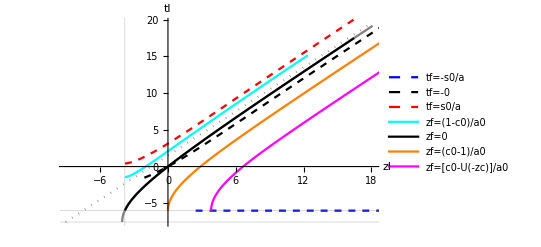

```mathematica
w00=1.2;
a0=0.2; (* a0 cannot be zero *)
(* Derived parameters *)
c0=Cosh[w00];
s0=Sinh[w00];
(* Bounds of axis *)
z0=c0/a0;
zc0=zlC[w00,a0];
(* Trajectory of particle "0" and asymptotics *)
pl=Plot[{(Sqrt[(a0*zl+c0)^2-1]-s0)/a0,zl+(c0-s0)/a0},{zl,-z0,2z0},GridLines->{{zc0}, {-s0/a0,-w00/a0}},AxesLabel->{"zl","tl"},PlotStyle->{Gray,Directive[Dotted,Gray]}];
(* Lines for tf= -s0/a0, 0, and +s0/a0, zf max is limited by Rindler horizon *)
ptn=PlotTF[-s0/a0,w00,a0,Directive[Dashed,Blue],"tf=-s0/a"];
pt0=PlotTF[0,w00,a0,Directive[Dashed,Black],"tf=-0"];
ptp=PlotTF[s0/a0,w00,a0,Directive[Dashed,Red],"tf=s0/a"];
(* Lines for zf= 0, (c0-1)/a0, 0, and (c0-U(-zc))/a0, zf max is limited by Rindler horizon *)
pzn=PlotZF[(1-c0)/a0,w00,a0,Cyan,"zf=(1-c0)/a0"];
pz0=PlotZF[0,w00,a0,Black,"zf=0"];
pzp1=PlotZF[(c0-1)/a0,w00,a0,Orange,"zf=(c0-1)/a0"];
pzp2=PlotZF[(c0-Uz[-zc0,w00,a0])/a0,w00,a0,Magenta,"zf=[c0-U(-zc)]/a0"];
(* Show all *)
Show[pl,ptn,pt0,ptp,pzn,pz0,pzp1,pzp2]
```

```mathematica
(* Check coordinate inversion *)
w00=1.2;
a0=0.2; (* a0 cannot be zero *)
(* Bounds of axis *)
z0=c0/a0;
zc0=zlC[w00,a0];
tc0=-w00/a0;
(* Plot zl for the inversion pair *)
Plot3D[ZL[TF[tl,zl,w00,a0],ZF[tl,zl,w00,a0],w00,a0],{zl,zc0,z0},{tl,tc0,z0},AxesLabel->{"zl","tl","zl(l→f→l)"},PlotLegends->Automatic]
(* Plot tl for the inversion pair *)
Plot3D[TL[TF[tl,zl,w00,a0],ZF[tl,zl,w00,a0],w00,a0],{zl,zc0,z0},{tl,tc0,z0},AxesLabel->{"zl","tl","tl(l→f→l)"},PlotLegends->Automatic]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*****************************************)
(* Geodesice of the metric *)
(*****************************************)
```

```mathematica
(* Plot geodesics when only aG0≠0 *)
PlotGeodesics[tmax_,zl1_,b1_,w0_,a_]:=Module[
{pl,pf},
(* Plot in lab frame *)
pl=ParametricPlot[{{ZtGeodesics[t,zl1,b1,w0,a][[1]],t},{ZL[t,ZtGeodesics[t,zl1,b1,w0,a][[2]],w0,a],TL[t,ZtGeodesics[t,zl1,b1,w0,a][[2]],w0,a]}},{t,-tmax/2,tmax},AxesLabel->{"zl","tl"},PlotStyle->{Black,Directive[Dashed,Orange]},PlotLegends->{"zl","zf→zl"} ,Epilog->{PointSize[Large],Red,Tooltip[#,#[[1]]]&@Point[{ZtGeodesics[0,zl1,b1,w0,a][[1]],0}]}];
(* Plot in free-fall frame, mark Rindler horizon *)
pf=ParametricPlot[{{ZtGeodesics[t,zl1,b1,w0,a][[2]],t},{ZF[t,ZtGeodesics[t,zl1,b1,w0,a][[1]],w0,a],TF[t,ZtGeodesics[t,zl1,b1,w0,a][[1]],w0,a]},{zfRindler[t,w0,a],t}},{t,-tmax/2,tmax},AxesLabel->{"zf","tf"},PlotStyle->{Black,Directive[Dashed,Orange],Directive[Gray,Dotted]},PlotLegends->{"zf","zl→zf","Rindler"},Epilog->{PointSize[Large],Red,Tooltip[#,#[[1]]]&@Point[{ZtGeodesics[0,zl1,b1,w0,a][[2]],0}]}];
Return[{pl,pf}]
]
```

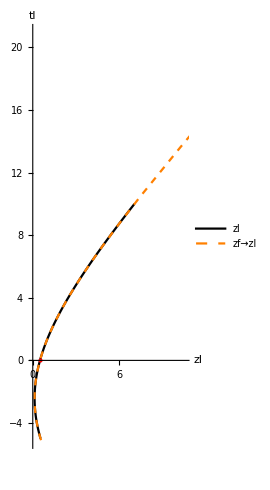

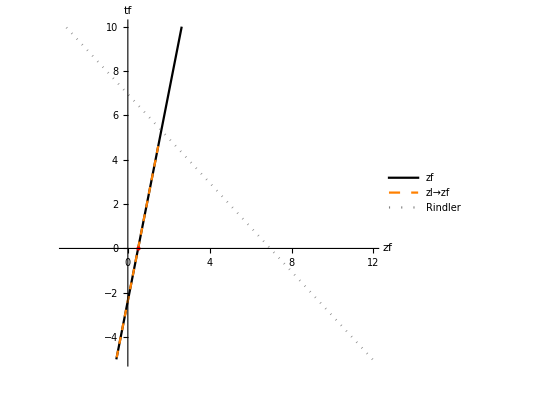

```mathematica
(* Check time-like geodesice *)
w00=0.1;
a0=0.13; 
zl11=0.5;
b11=0.3;
{pl,pf}=PlotGeodesics[10,zl11,b11,w00,a0];
Show[pl]
Show[pf]
```

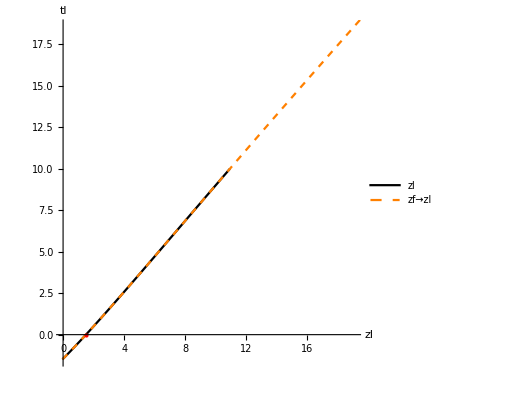

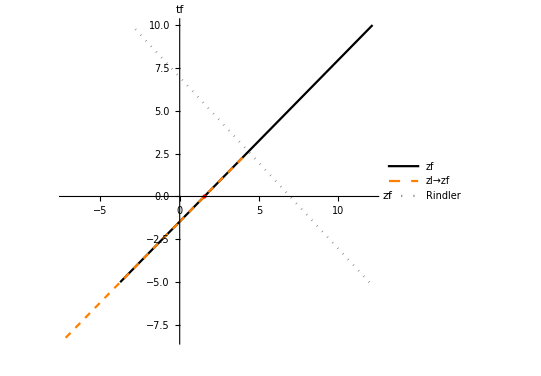

```mathematica
(* Check light-like geodesice *)
w00=0.1;
a0=0.13; 
zl11=1.5;
{pl,pf}=PlotGeodesics[10,zl11,1,w00,a0];
Show[pl]
Show[pf]
```

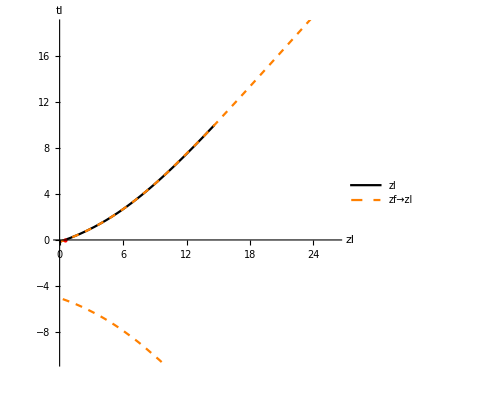

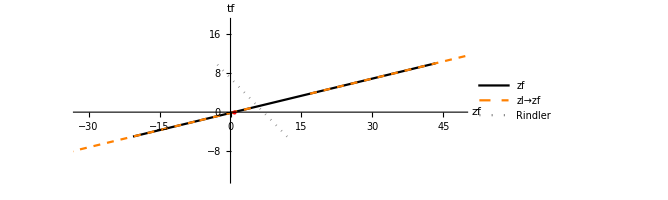

```mathematica
(* Check space-like geodesice *)
w00=0.1;
a0=0.13; 
zl11=0.5;
b11=3;
{pl,pf}=PlotGeodesics[10,zl11,b11,w00,a0];
Show[pl]
Show[pf]
```

```mathematica
(*****************************************)
(* Motion of test particles *)
(*****************************************)
```

```mathematica
(* Integrate velocity to find trajectory from t=0 to t=tmax in the lab frame *)
(* Plot trajectories in both frame and check acceleration in lab frame *)
ZLtPlots[tmax_,zl1_,b1_,w0_,aE0_,aG0_,aM0_]:=Module[
{s,z,pl,pf,pb,pa},
(* Numerical solution *)
s=NDSolve[{z'[t]==Bz1[z[t],zl1,b1,w0,aE0,aG0,aM0],z[0]==zl1},z,{t,0,tmax}];
(* Plot solution in lab frame *)
pl=ParametricPlot[Evaluate[{z[t],t}/.s],{t,0,tmax},PlotRange->All,AxesLabel->{"zl","tl"},PlotStyle->Directive[Blue,Thickness[0.01]],PlotLegends->{"Numeric"}];
(* Plot solution in free-fall frame *)
pf=ParametricPlot[Evaluate[{ZF[t,z[t],w0,aG0],TF[t,z[t],w0,aG0]}/.s],{t,0,tmax},PlotRange->All,AxesLabel->{"zf","tf"},PlotStyle->Directive[Blue,Thickness[0.01]],PlotLegends->{"Numeric"}];
(* Plot to check velocity in lab frame *)
pb=Plot[Evaluate[{z'[t],Bz1[z[t],zl1,b1,w0,aE0,aG0,aM0]}/.s],{t,0,tmax},PlotRange->All,PlotLegends->{"z'[t]","b[z]"},AxesLabel->{"t","β"},PlotStyle->{Black,Dashed},GridLines->{None, {1}}];
(* Plot to check acceleration in lab frame *)
pa=Plot[Evaluate[{z''[t],Azb[z[t],z'[t],w0,aE0,aG0,aM0]}/.s],{t,tmax/10^3,tmax},PlotRange->All,PlotLegends->{"z''[t]","a[z,b]"},AxesLabel->{"t","a"},PlotStyle->{Black,Dashed}];
Return[{s,{pl,pf,pb,pa}}]
]
```

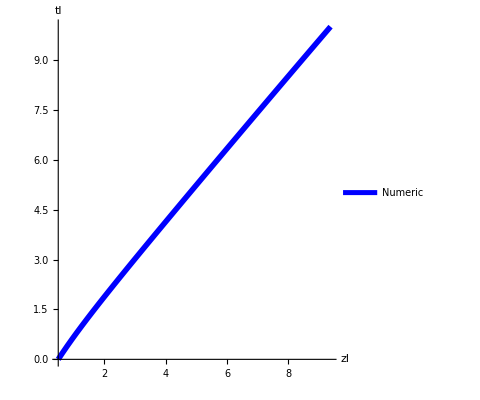

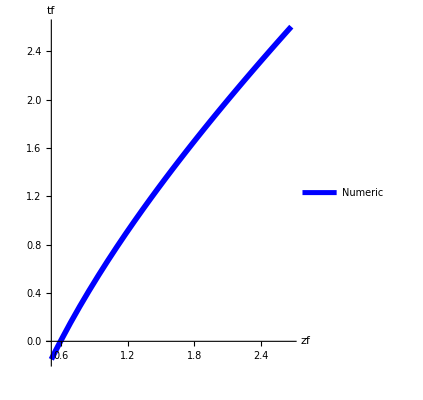

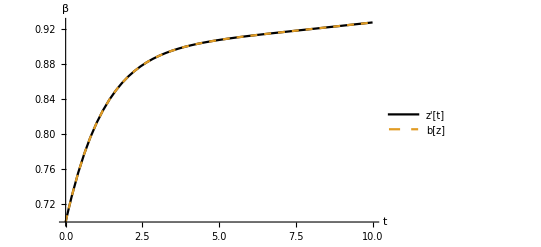

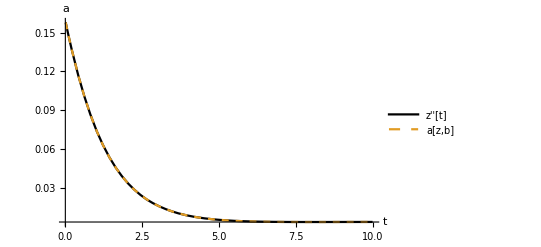

```mathematica
(* Check consistency of accelerations *)
w00=0.3;
aE00=0.2;
aM00=0.1;
aG00=0.13; (* aG0 cannot be zero *)
(* Initial conditions *)
zl11=0.5;
b11=0.7;
{s,{pl,pf,pb,pa}}=ZLtPlots[10,zl11,b11,w00,aE00,aG00,aM00];
(* Lab frame trajectory *)
Show[pl]
(* Free-fall frame trajectory *)
Show[pf]
(* Lab frame velocity *)
Show[pb]
(* Lab frame acceleration *)
Show[pa]
```

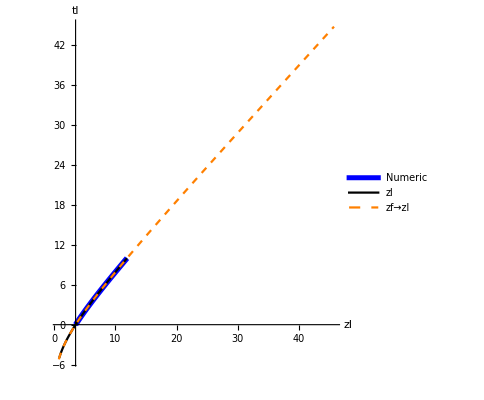

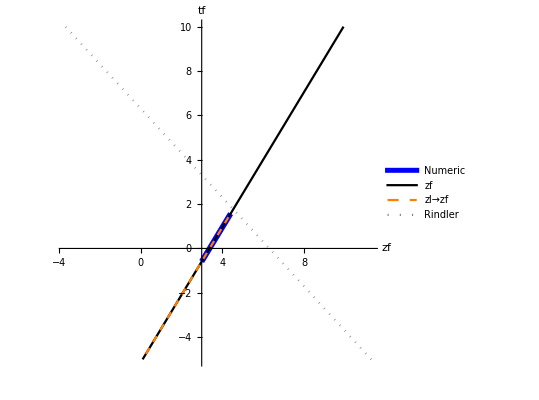

```mathematica
(* Trajectories when only aG0≠0 *)
(* Compare with geodesics *)
w00=0.2;
aG00=0.13; (* aG0 cannot be zero *)
(* Initial conditions *)
zl11=3.5;
b11=0.7;
tmax=10;
(* Trajectory from numerical integration *)
{s,{pl,pf,pb,pa}}=ZLtPlots[tmax,zl11,b11,w00,0,aG00,0];
(* Geodesics from analytical formula *)
{pla,pfa}=PlotGeodesics[tmax,zl11,b11,w00,aG00];
(* Lab frame *)
Show[pl,pla]
(* Free-fall frame *)
Show[pf,pfa]
```

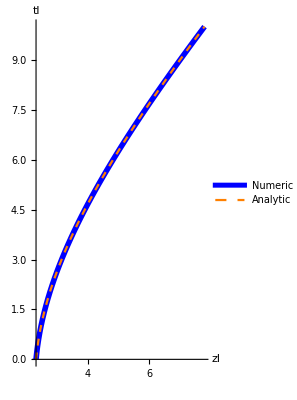

```mathematica
(* Trajectories when only aE0≠0 *)
(* Compare with analytical solution *)
w00=0.3;
aE00=0.13; 
(* Initial conditions *)
zl11=2.3;
b11=0.1;
tmax=10;
(* Trajectory from numerical integration *)
{s,{pl,pf,pb,pa}}=ZLtPlots[tmax,zl11,b11,w00,aE00,0,0];
(* Analytical solution *)
pla=ParametricPlot[{ZLtE[t,zl11,b11,aE00],t},{t,0,tmax},PlotStyle->Directive[Orange,Dashed],PlotLegends->{"Analytic"}];
(* Lab frame *)
Show[pl,pla]
```

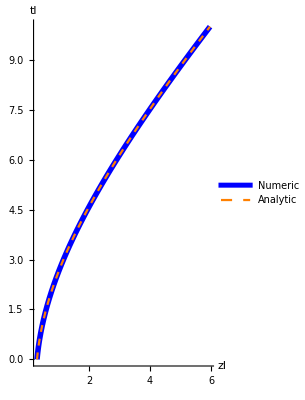

```mathematica
(* Trajectories when only aM0≠0 *)
(* Compare with analytical solution *)
w00=0.3;
aM00=0.15; 
(* Initial conditions *)
zl11=0.3;
b11=0.1;
tmax=10;
(* Trajectory from numerical integration *)
{s,{pl,pf,pb,pa}}=ZLtPlots[tmax,zl11,b11,w00,0,0,aM00];
(* Analytical solution *)
pla=ParametricPlot[{ZLtM[t,zl11,b11,w00,aM00],t},{t,0,tmax},PlotStyle->Directive[Orange,Dashed],PlotLegends->{"Analytic"}];
(* Lab frame *)
Show[pl,pla]
```

```mathematica
(* The exact acceleration can be written as a=aE+aG+aM *)
AE[zl_,b_,w0_,aE0_,aG0_,aM0_]:=aE0*DtauDt[zl,w0,aG0,b](1+aM0*zl/Cosh[w0])(1/Vz[zl,w0,aG0]^2-b^2/Uz[zl,w0,aG0]^2)
(*AE[zl,b,w0,aE0,aG0,aM0]*)
```

```mathematica
AG[zl_,b_,w0_,aG0_]:=aG0 (Uz[zl,w0,aG0]/Vz[zl,w0,aG0])(1+b^2(Tanh[z2Rho[zl,w0,aG0]]/(z2Rho[zl,w0,aG0]+Sinh[w0]-w0)^3-1/(1-1/(aG0*zl+Cosh[w0])^2)))
(*AG[zl,b,w0,aG0]*)
```

```mathematica
AM[zl_,b_,w0_,aG0_,aM0_]:=aM0/(aM0*zl+Cosh[w0])((Uz[zl,w0,aG0]/Vz[zl,w0,aG0])^2-b^2)
(*AM[zl,b,w0,aG0,aM0]*)
```

```mathematica
(* Check two expressions of acceleration are the same *)
FullSimplify[(AE[zl,b,w0,aE0,aG0,aM0]+AG[zl,b,w0,aG0]+AM[zl,b,w0,aG0,aM0]-Azb[zl,b,w0,aE0,aG0,aM0])/.{zl->3,b->EulerGamma,w0->Exp[1],aE0->5,aG0->Pi,aM0->Sqrt[2]}]
```

0

```mathematica
(* Check by plotting *)
w00=0.1;
aE00=0.32;
aG00=0.17;
aM00=0.13;
Plot3D[AE[zl,b,w00,aE00,aG00,aM00]+AG[zl,b,w00,aG00]+AM[zl,b,w00,aG00,aM00]-Azb[zl,b,w00,aE00,aG00,aM00],{zl,0,3},{b,0,1},AxesLabel->{"zl","b"}]
```

-Graphics3D-

```mathematica
(* Check asymptotics of residual acceleration *)
a0=aG0+aM0/Cosh[w0]
b0=aG0/Cosh[w0]/(1+Cosh[w0])
```

aG0+aM0 Sech[w0]

(aG0 Sech[w0])/(1+Cosh[w0])

```mathematica
(* Asymptotic accelerations when zl1=0 *)
arz0=b1^2(a0/2-b0)-3a0/8b1^4
```

-3/8 b1^4 (aG0+aM0 Sech[w0])+b1^2 (-(aG0 Sech[w0])/(1+Cosh[w0])+1/2 (aG0+aM0 Sech[w0]))

```mathematica
arz=aRz[b1,w0,aG0,aM0]
```

aM0 (1-b1^2) Sech[w0]+(1-(3 b1^2)/2+(3 b1^4)/8) (-aG0-aM0 Sech[w0])+aG0 (1-b1^2 (1+Sech[w0]/(1+Cosh[w0])))

```mathematica
FullSimplify[arz0-arz]
```

0

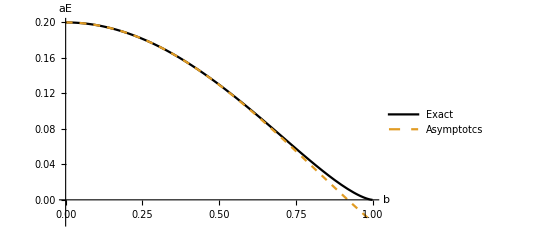

```mathematica
(* Acceleration due to E field at zl1=0 *)
(*AE[zl,b,w0,aE0,aG0,aM0]*)
w00=0.1;
aE00=0.2;
aG00=0.3;
aM00=0.15;
Plot[{AE[0,b1,w00,aE00,aG00,aM00],aEz[b1,aE00]},{b1,0,1},AxesLabel->{"b","aE"},PlotLegends->{"Exact","Asymptotcs"},PlotStyle->{Black,Dashed}]
```

```mathematica
Plot3D[{AE[0,b1,w0,aE00,aG00,aM00],aEz[b1,aE00]},{b1,0,1},{w0,0,0.2},AxesLabel->{"b","w0","aE"},PlotLegends->{"Exact","Asymptotcs"}]
```

-Graphics3D-

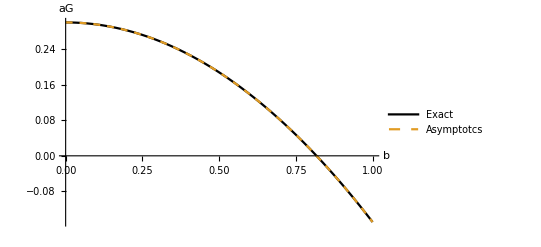

```mathematica
(* Acceleration due to metric at zl1=0 *)
(*AG[zl,b,w0,aG0]*)
w00=0.1;
aG00=0.3;
Plot[{AG[0,b1,w00,aG00],aGz[b1,w00,aG00]},{b1,0,1},AxesLabel->{"b","aG"},PlotLegends->{"Exact","Asymptotcs"},PlotStyle->{Black,Dashed}]
```

-Graphics3D-

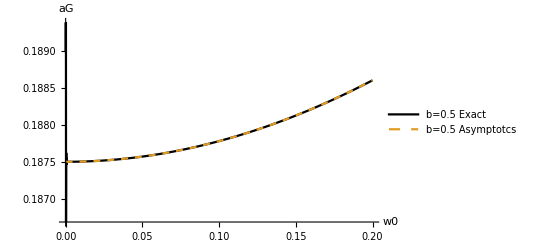

```mathematica
b11=0.5;
Plot3D[{AG[0,b1,w0,aG00],aGz[b1,w0,aG00]},{b1,0,1},{w0,0,0.2},AxesLabel->{"b","w0","aG"},PlotLegends->{"Exact","Asymptotcs"}]
Plot[{AG[0,b11,w0,aG00],aGz[b11,w0,aG00]},{w0,0,0.2},AxesLabel->{"w0","aG"},PlotLegends->{Row[{"b=",b11," Exact"}],Row[{"b=",b11," Asymptotcs"}]},PlotStyle->{Black,Dashed}]
```

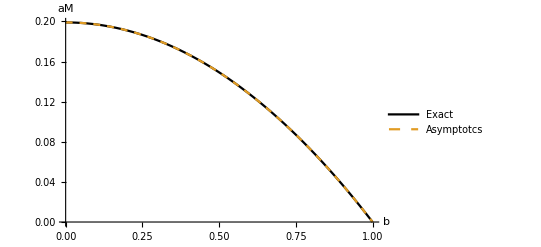

```mathematica
(* Acceleration due to mass alone at zl1=0 *)
(*AM[zl,b,w0,aG0,aM0]*)
w00=0.1;
aG00=0.3;
aM00=0.2;
Plot[{AM[0,b1,w00,aG00,aM00],aMz[b1,w00,aM00]},{b1,0,1},AxesLabel->{"b","aM"},PlotLegends->{"Exact","Asymptotcs"},PlotStyle->{Black,Dashed}]
```

```mathematica
Plot3D[{AM[0,b1,w0,aG00,aM00],aMz[b1,w0,aM00]},{b1,0,1},{w0,0,0.2},AxesLabel->{"b","w0","aM"},PlotLegends->{"Exact","Asymptotcs"}]
```

-Graphics3D-

```mathematica
(* Asymptotic accelerations when b1=0 *)
(* b0=0 *)
arb0=-h1(2a0^2-(2a0+b0)aG0+7aG0^2/6)
(* b0≠0 *)
arbn=-h1(2a0^2-(2a0+b0)aG0+aG0^2)
```

-h1 ((7 aG0^2)/6+2 (aG0+aM0 Sech[w0])^2-aG0 ((aG0 Sech[w0])/(1+Cosh[w0])+2 (aG0+aM0 Sech[w0])))

-h1 (aG0^2+2 (aG0+aM0 Sech[w0])^2-aG0 ((aG0 Sech[w0])/(1+Cosh[w0])+2 (aG0+aM0 Sech[w0])))

```mathematica
FullSimplify[aRb[h1,Pi,aG0,aM0]-arbn/.w0->Pi]
```

0

```mathematica
FullSimplify[aRb[h1,0,aG0,aM0]-arb0/.w0->0]
```

0

```mathematica
Series[Azb[h1,0,0,-aG0-aM0,aG0,aM0],{h1,0,1}]
```

(-(2 aG0^2)/3-2 aG0 aM0-2 aM0^2) h1+O[h1]^(3/2)

```mathematica
FullSimplify[Series[Azb[h1,0,w0,-aG0-aM0/Cosh[w0],aG0,aM0]/.w0->Pi,{h1,0,1}]]
```

(aG0^2 (-1-Csch[π]^2 (-1+Sech[π]))-2 aG0 aM0 Sech[π]-2 aM0^2 Sech[π]^2) h1+O[h1]^2

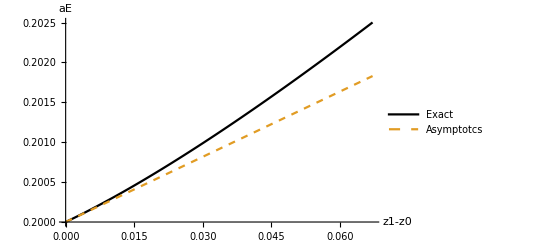

```mathematica
(* Acceleration due to E field at b1=0 *)
(* AE[zl,b,w0,aE0,aG0,aM0]*)
w00=0.2; (* w0≠0: asymptotics valid when aG0*zl1<<Sinh[w0] *)
aE00=0.2;
aG00=0.3;
aM00=0.13;
zmax=Sinh[w00]/aG00/10;
Plot[{AE[zl1,0,w00,aE00,aG00,aM00],aEb[zl1,w00,aE00,aG00,aM00]},{zl1,0,zmax},AxesLabel->{"z1-z0","aE"},PlotLegends->{"Exact","Asymptotcs"},PlotStyle->{Black,Dashed}]
```

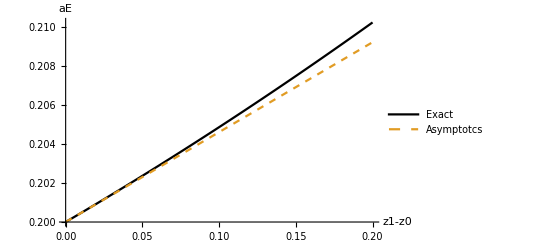

```mathematica
(* w0=0 *)
Plot[{AE[zl1,0,0,aE00,aG00,aM00],aEb[zl1,0,aE00,aG00,aM00]},{zl1,0,0.2},AxesLabel->{"z1-z0","aE"},PlotLegends->{"Exact","Asymptotcs"},PlotStyle->{Black,Dashed}]
```

```mathematica
FullSimplify[Series[AE[zl1,0,w0,aE0,aG0,aM0]-aEb[zl1,w0,aE0,aG0,aM0],{zl1,0,1}]/.w0->Pi]
```

O[zl1]^2

```mathematica
FullSimplify[Series[AE[zl1,0,w0,aE0,aG0,aM0]-aEb[zl1,w0,aE0,aG0,aM0],{zl1,0,1}]/.w0->0]
```

O[zl1]^2

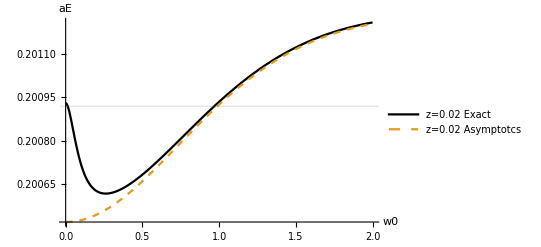

```mathematica
zl11=0.02;
Plot[{AE[zl11,0,w0,aE00,aG00,aM00],aEb[zl11,w0,aE00,aG00,aM00]},{w0,0,2},AxesLabel->{"w0","aE"},PlotLegends->{Row[{"z=",zl11," Exact"}],Row[{"z=",zl11," Asymptotcs"}]},PlotStyle->{Black,Dashed},GridLines->{{Sinh[w00]/aG00}, {aEb[zl11,0,aE00,aG00,aM00]}}]
```

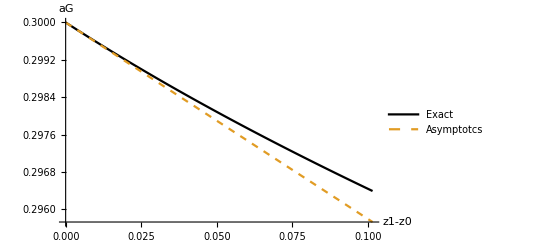

```mathematica
(* Acceleration due to metric at b1=0 *)
(*AG[zl,b,w0,aG0]*)
w00=0.3; (* w0≠0: asymptotics valid when aG0*zl1<<Sinh[w0] *)
aG00=0.3;
zmax=Sinh[w00]/aG00/10;
Plot[{AG[zl1,0,w00,aG00],aGb[zl1,w00,aG00]},{zl1,0,zmax},AxesLabel->{"z1-z0","aG"},PlotLegends->{"Exact","Asymptotcs"},PlotStyle->{Black,Dashed}]
```

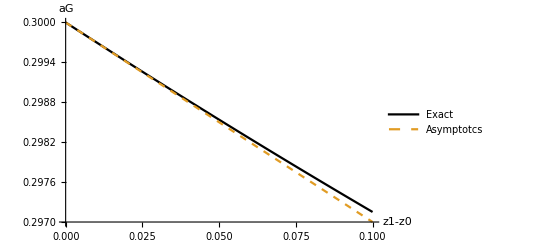

```mathematica
(* w0=0 *)
Plot[{AG[zl1,0,0,aG00],aGb[zl1,0,aG00]},{zl1,0,0.1},AxesLabel->{"z1-z0","aG"},PlotLegends->{"Exact","Asymptotcs"},PlotStyle->{Black,Dashed}]
```

```mathematica
FullSimplify[Series[AG[zl1,0,w0,aG0]-aGb[zl1,w0,aG0],{zl1,0,1}]/.w0->Pi]
```

O[zl1]^2

```mathematica
FullSimplify[Series[AG[zl1,0,w0,aG0],{zl1,0,1}]/.w0->0]
```

Indeterminate+Indeterminate zl1+O[zl1]^2

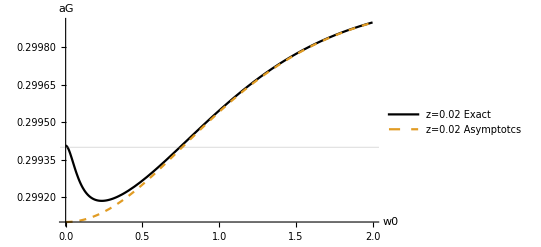

```mathematica
zl11=0.02;
Plot[{AG[zl11,0,w0,aG00],aGb[zl11,w0,aG00]},{w0,0,2},AxesLabel->{"w0","aG"},PlotLegends->{Row[{"z=",zl11," Exact"}],Row[{"z=",zl11," Asymptotcs"}]},PlotStyle->{Black,Dashed},GridLines->{{Sinh[w00]/aG00}, {aGb[zl11,0,aG00]}}]
```

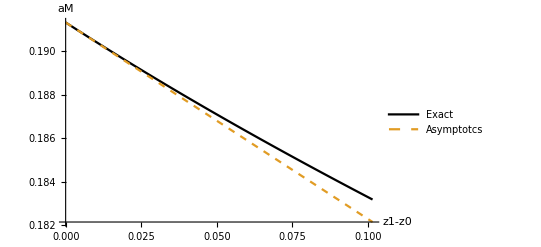

```mathematica
(* Acceleration due to mass at b1=0 *)
(*AM[zl,b,w0,aG0,aM0]*)
w00=0.3; (* w0≠0: asymptotics valid when aG0*zl1<<Sinh[w0] *)
aG00=0.3;
aM00=0.2;
zmax=Sinh[w00]/aG00/10;
Plot[{AM[zl1,0,w00,aG00,aM00],aMb[zl1,w00,aG00,aM00]},{zl1,0,zmax},AxesLabel->{"z1-z0","aM"},PlotLegends->{"Exact","Asymptotcs"},PlotStyle->{Black,Dashed}]
```

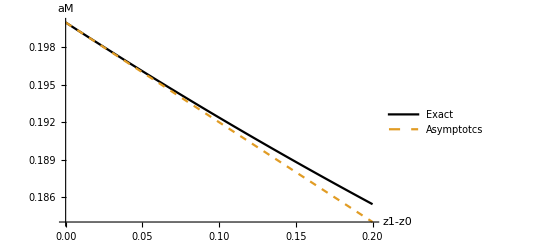

```mathematica
(* w0=0 *)
aG00=0.3;
aM00=0.2;
zmax=0.2;
Plot[{AM[zl1,0,0,aG00,aM00],aMb[zl1,0,aG00,aM00]},{zl1,0,zmax},AxesLabel->{"z1-z0","aM"},PlotLegends->{"Exact","Asymptotcs"},PlotStyle->{Black,Dashed}]
```

```mathematica
FullSimplify[Series[AM[zl1,0,w0,aG0,aM0]-aMb[zl1,w0,aG0,aM0],{zl1,0,1}]/.w0->Pi]
```

O[zl1]^2

```mathematica
FullSimplify[Series[AM[zl1,0,w0,aG0,aM0]-aMb[zl1,w0,aG0,aM0],{zl1,0,1}]/.w0->0]
```

O[zl1]^2

0.004

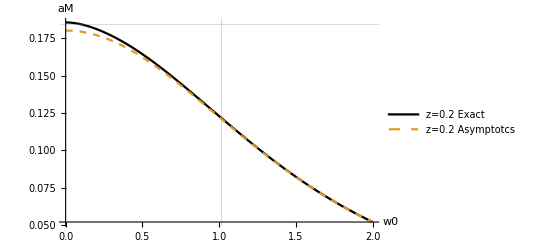

```mathematica
zl11=0.2;
aM00*aG00*zl11/3
Plot[{AM[zl11,0,w0,aG00,aM00],aMb[zl11,w0,aG00,aM00]},{w0,0,2},AxesLabel->{"w0","aM"},PlotLegends->{Row[{"z=",zl11," Exact"}],Row[{"z=",zl11," Asymptotcs"}]},PlotStyle->{Black,Dashed},GridLines->{{Sinh[w00]/aG00}, {aMb[zl11,0,aG00,aM00]}}]
```